```mathematica
Clear["`*"];
(*Exogenous location choice*)
payoffm = 1-(1-ψ)/(2 q)+((ψ-q)/(1-2 q))^2;
payoffl = (ψ-q)/(1-2 q)+1/2 (1-(1-ψ)/(2 q))^2;
eqmeqn = Simplify[payoffm==payoffl, 0<q<1/2];
payoffmfunction[ψ_,q_] = payoffm ;
payofflfunction[ψ_,q_] = payoffl;
totalrent = Simplify[(1-2*q)*payoffm+2*q*payoffl, 0<q<1/2];
totalrentfunction[ψ_,q_] = totalrent;
```

```mathematica
(*Full closed form solution, put in appendix
*)
Solve[payofflfunction[ψ,q]==payoffmfunction[ψ,q], q][[1]]// Lookup[#,q]&
```

1/4-1/2 √(1/4-ψ^2/3+ψ^4/(3 2^(2/3) (27-162 ψ+351 ψ^2-324 ψ^3+108 ψ^4+2 ψ^6-3 √3 √(27-324 ψ+1674 ψ^2-4860 ψ^3+8667 ψ^4-9720 ψ^5+6700 ψ^6-2616 ψ^7+484 ψ^8-48 ψ^9+16 ψ^10))^(1/3))+((27-162 ψ+351 ψ^2-324 ψ^3+108 ψ^4+2 ψ^6-3 √3 √(27-324 ψ+1674 ψ^2-4860 ψ^3+8667 ψ^4-9720 ψ^5+6700 ψ^6-2616 ψ^7+484 ψ^8-48 ψ^9+16 ψ^10))^(1/3))/(6 2^(1/3)))-1/2 √(1/2-(2 ψ^2)/3-ψ^4/(3 2^(2/3) (27-162 ψ+351 ψ^2-324 ψ^3+108 ψ^4+2 ψ^6-3 √3 √(27-324 ψ+1674 ψ^2-4860 ψ^3+8667 ψ^4-9720 ψ^5+6700 ψ^6-2616 ψ^7+484 ψ^8-48 ψ^9+16 ψ^10))^(1/3))-((27-162 ψ+351 ψ^2-324 ψ^3+108 ψ^4+2 ψ^6-3 √3 √(27-324 ψ+1674 ψ^2-4860 ψ^3+8667 ψ^4-9720 ψ^5+6700 ψ^6-2616 ψ^7+484 ψ^8-48 ψ^9+16 ψ^10))^(1/3))/(6 2^(1/3))-(1-2 ψ^2-4 (1-2 ψ+ψ^2))/(4 √(1/4-ψ^2/3+ψ^4/(3 2^(2/3) (27-162 ψ+351 ψ^2-324 ψ^3+108 ψ^4+2 ψ^6-3 √3 √(27-324 ψ+1674 ψ^2-4860 ψ^3+8667 ψ^4-9720 ψ^5+6700 ψ^6-2616 ψ^7+484 ψ^8-48 ψ^9+16 ψ^10))^(1/3))+((27-162 ψ+351 ψ^2-324 ψ^3+108 ψ^4+2 ψ^6-3 √3 √(27-324 ψ+1674 ψ^2-4860 ψ^3+8667 ψ^4-9720 ψ^5+6700 ψ^6-2616 ψ^7+484 ψ^8-48 ψ^9+16 ψ^10))^(1/3))/(6 2^(1/3)))))

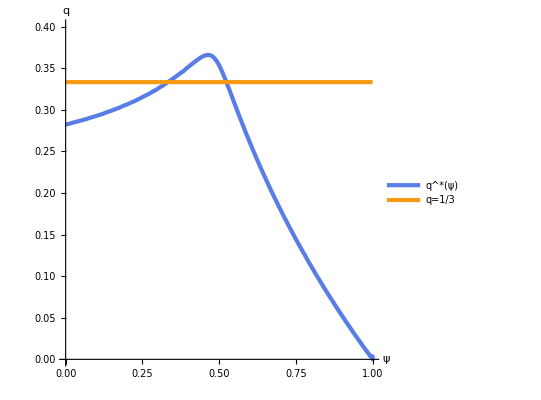

```mathematica
(* Plot of exogenous choice solution - uncoordinated*)
ContourPlot[{payofflfunction[ψ,q]==payoffmfunction[ψ,q],q==1/3},{ψ,0,1},{q,0,0.4},PlotTheme->"Business",PlotLegends->{"\!\(\*SuperscriptBox[q, \(*\)]\)(ψ)","\!\(q\)=\!\(\*FractionBox[\(1\), \(3\)]\)"},Frame->False,Axes->True,AxesLabel->{ψ,q}]
```

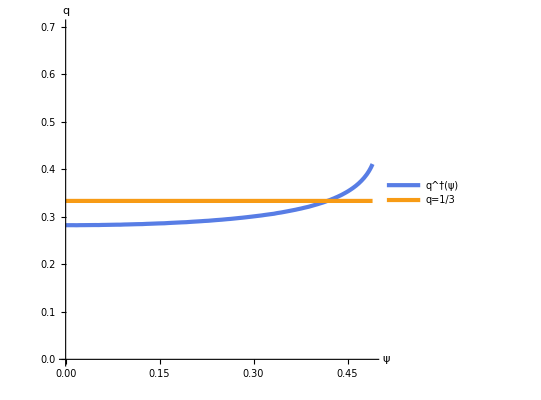

```mathematica
(*Workers united to maximize total rent*)
focfunction[ψ_,q_] = Derivative[0,1][totalrentfunction][ψ,q] // Simplify[#,  0<q<1/2]&;
ContourPlot[{focfunction[ψ,q]==0 ,q==1/3}, {ψ,0,0.49},{q,0,0.7} ,Frame->False,Axes->True,AxesLabel->{ψ,q},
PlotTheme->"Business", PlotLegends->{"q^†(ψ)","q=1/3"}]
```

```mathematica
(*Range of ψ to 1/2*)
Solve[focfunction[ψ,1/3]==0,ψ]//Lookup[#,ψ]& //Select[#,#>0&] &
```

{(√(11/7))/3}